```mathematica
(*Before you run the file,every time,go to evaluation->Quit Kernel->Local
and then start the evaluation process.*)
```

#### { RowBox[{"SetOptions", "[", RowBox[{"Plot", ",", RowBox[{"BaseStyle", "->", RowBox[{"{", RowBox[{ RowBox[{"Font

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True];SetOptions[DensityPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True];wstate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1+s2+s3==1,1/Sqrt[3],0]*If[s1p+s2p+s3p==1,1/Sqrt[3],0];
ghzstate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[(s1==s2)&&(s2==s3),1/Sqrt[2],0]*If[(s1p==s2p)&&(s2p==s3p),1/Sqrt[2],0];
starstatec[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[((s1==s2)&&(s2==s3))||((s1==1)&&(s2==0)),1/2,0]*If[((s1p==s2p)&&(s2p==s3p))||((s1p==1)&&(s2p==0)),1/2,0];
starstatea[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[((s1==s2)&&(s2==s3))||((s3==1)&&(s2==0)),1/2,0]*If[((s1p==s2p)&&(s2p==s3p))||((s3p==1)&&(s2p==0)),1/2,0];
carstate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[(s1+s2+s3==1)||((s1==1)&&(s2==1)&&(s3==1)),1/2,0]*If[(s1p+s2p+s3p==1)||((s1p==1)&&(s2p==1)&&(s3p==1)),1/2,0];
psistate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=Which[((s1==0)&&(s2==0)&&(s3==1))||((s1==0)&&(s2==1)&&(s3==0)),1/Sqrt[6],((s1==1)&&(s2==0)&&(s3==0)),-Sqrt[2/3],True,0]*Which[((s1p==0)&&(s2p==0)&&(s3p==1))||((s1p==0)&&(s2p==1)&&(s3p==0)),1/Sqrt[6],((s1p==1)&&(s2p==0)&&(s3p==0)),-Sqrt[2/3],True,0];
zerozerozerostate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[(s1==0)&&(s2==0)&&(s3==0),1,0]*If[(s1p==0)&&(s2p==0)&&(s3p==0),1,0];
onezerozerostate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[(s1==1)&&(s2==0)&&(s3==0),1,0]*If[(s1p==1)&&(s2p==0)&&(s3p==0),1,0];
onepluszerostate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[(s1==1)&&(s3==0),1,0]*If[(s1p==1)&&(s3p==0),1,0]*(1/2);
mathieustate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[((s1==s2)&&(s2==s3))||((s1==1)&&(s2==1)&&(s3==0)),1/Sqrt[3],0]*If[((s1p==s2p)&&(s2p==s3p))||((s1p==1)&&(s2p==1)&&(s3p==0)),1/Sqrt[3],0];
plusplusplusstate[s1p_,s2p_,s3p_,s1_,s2_,s3_]=1/8;
plusplusstateab[s1p_,s2p_,s3p_,s1_,s2_,s3_]=(1/4)*If[s3==0,1,0]*If[s3p==0,1,0];
plusplusstateac[s1p_,s2p_,s3p_,s1_,s2_,s3_]=(1/4)*If[s2==0,1,0]*If[s2p==0,1,0];
plusplusstatebc[s1p_,s2p_,s3p_,s1_,s2_,s3_]=(1/4)*If[s1==0,1,0]*If[s1p==0,1,0];
bellab[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1==s2,1/Sqrt[2],0]*If[s1p==s2p,1/Sqrt[2],0]*If[s3==0,1,0]*If[s3p==0,1,0];
bellac[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1==s3,1/Sqrt[2],0]*If[s1p==s3p,1/Sqrt[2],0]*If[s2==0,1,0]*If[s2p==0,1,0];
bellbc[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s2==s3,1/Sqrt[2],0]*If[s2p==s3p,1/Sqrt[2],0]*If[s1==0,1,0]*If[s1p==0,1,0];
id[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1p==s1,1/2,0]*If[s2p==s2,1/2,0]*If[s3p==s3,1/2,0];
ρabc[s1p_,s2p_,s3p_,s1_,s2_,s3_]=μ*(wstate[s1p,s2p,s3p,s1,s2,s3])+(1-μ)*id[s1p,s2p,s3p,s1,s2,s3];
Pa1[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s2p==s2,1,0]*If[s3p==s3,1,0]*If[s1==0,Cos[θ1],Exp[I*ϕ1]*Sin[θ1]]*If[s1p==0,Cos[θ1],Exp[-I*ϕ1]*Sin[θ1]];
Pa2[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s2p==s2,1,0]*If[s3p==s3,1,0]*If[s1==0,Sin[θ1],-Exp[-I*ϕ1]*Cos[θ1]]*If[s1p==0,Sin[θ1],-Exp[I*ϕ1]*Cos[θ1]];
Pa1b1[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1p==s1,1,0]*If[s3p==s3,1,0]*If[s2==0,Cos[θ2],Exp[I*ϕ2]*Sin[θ2]]*If[s2p==0,Cos[θ2],Exp[-I*ϕ2]*Sin[θ2]];
Pa1b2[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1p==s1,1,0]*If[s3p==s3,1,0]*If[s2==0,Sin[θ2],-Exp[-I*ϕ2]*Cos[θ2]]*If[s2p==0,Sin[θ2],-Exp[I*ϕ2]*Cos[θ2]];
Pa2b1[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1p==s1,1,0]*If[s3p==s3,1,0]*If[s2==0,Cos[θ3],Exp[I*ϕ3]*Sin[θ3]]*If[s2p==0,Cos[θ3],Exp[-I*ϕ3]*Sin[θ3]];
Pa2b2[s1p_,s2p_,s3p_,s1_,s2_,s3_]=If[s1p==s1,1,0]*If[s3p==s3,1,0]*If[s2==0,Sin[θ3],-Exp[-I*ϕ3]*Cos[θ3]]*If[s2p==0,Sin[θ3],-Exp[I*ϕ3]*Cos[θ3]];
entropy[sigma_]:=-N[DeleteCases[Chop[Eigenvalues[sigma]],0].Log[2,DeleteCases[Chop[Eigenvalues[sigma]],0]]];
lastabs[ls_]:=Abs[Last[ls]];
```

```mathematica
rhoabc={};
proja1={};
proja2={};
proja1b1={};
proja1b2={};
proja2b1={};
proja2b2={};
For[s1=0,s1≤1,s1=s1+1,
For[s2=0,s2≤1,s2=s2+1,
For[s3=0,s3≤1,s3=s3+1,
rhoabcline={};
proja1line={};
proja2line={};
proja1b1line={};
proja1b2line={};
proja2b1line={};
proja2b2line={};
For[s1p=0,s1p≤1,s1p=s1p+1,
For[s2p=0,s2p≤1,s2p=s2p+1,
For[s3p=0,s3p≤1,s3p=s3p+1,
rhoabcline=Append[rhoabcline,ρabc[s1p,s2p,s3p,s1,s2,s3]];
proja1line=Append[proja1line,Pa1[s1p,s2p,s3p,s1,s2,s3]];
proja2line=Append[proja2line,Pa2[s1p,s2p,s3p,s1,s2,s3]];
proja1b1line=Append[proja1b1line,Pa1b1[s1p,s2p,s3p,s1,s2,s3]];
proja1b2line=Append[proja1b2line,Pa1b2[s1p,s2p,s3p,s1,s2,s3]];
proja2b1line=Append[proja2b1line,Pa2b1[s1p,s2p,s3p,s1,s2,s3]];
proja2b2line=Append[proja2b2line,Pa2b2[s1p,s2p,s3p,s1,s2,s3]];
];
];
];
rhoabc=Append[rhoabc,rhoabcline];
proja1=Append[proja1,proja1line];
proja2=Append[proja2,proja2line];
proja1b1=Append[proja1b1,proja1b1line];
proja1b2=Append[proja1b2,proja1b2line];
proja2b1=Append[proja2b1,proja2b1line];
proja2b2=Append[proja2b2,proja2b2line];
];
];
];
rhomeas1=proja1.rhoabc.proja1;
rhomeas2=proja2.rhoabc.proja2;
rhoabcM1=rhomeas1+rhomeas2;
rhomeas11=proja1b1.proja1.rhoabc.proja1.proja1b1;
rhomeas12=proja1b2.proja1.rhoabc.proja1.proja1b2;
rhomeas21=proja2b1.proja2.rhoabc.proja2.proja2b1;
rhomeas22=proja2b2.proja2.rhoabc.proja2.proja2b2;
rhoabcM2=rhomeas11+rhomeas12+rhomeas21+rhomeas22;

rhoac=Table[0,{n,1,4},{np,1,4}];
rhobc=Table[0,{n,1,4},{np,1,4}];
rhoab=Table[0,{n,1,4},{np,1,4}];
rhoa=Table[0,{n,1,2},{np,1,2}];
rhob=Table[0,{n,1,2},{np,1,2}];
rhoc=Table[0,{n,1,2},{np,1,2}];
rhoacM1=Table[0,{n,1,4},{np,1,4}];
rhobcM1=Table[0,{n,1,4},{np,1,4}];
rhoabM1=Table[0,{n,1,4},{np,1,4}];
rhoaM1=Table[0,{n,1,2},{np,1,2}];
rhobM1=Table[0,{n,1,2},{np,1,2}];
rhocM1=Table[0,{n,1,2},{np,1,2}];
rhoacM2=Table[0,{n,1,4},{np,1,4}];
rhobcM2=Table[0,{n,1,4},{np,1,4}];
rhoabM2=Table[0,{n,1,4},{np,1,4}];
rhoaM2=Table[0,{n,1,2},{np,1,2}];
rhobM2=Table[0,{n,1,2},{np,1,2}];
rhocM2=Table[0,{n,1,2},{np,1,2}];
For[s1=0,s1≤1,s1=s1+1,
For[s2=0,s2≤1,s2=s2+1,
For[s3=0,s3≤1,s3=s3+1,
nabc=4*s1+2*s2+s3+1;
nab=2*s1+s2+1;
nac=2*s1+s3+1;
nbc=2*s2+s3+1;
na=s1+1;
nb=s2+1;
nc=s3+1;
For[s1p=0,s1p≤1,s1p=s1p+1,
For[s2p=0,s2p≤1,s2p=s2p+1,
For[s3p=0,s3p≤1,s3p=s3p+1,
npabc=4*s1p+2*s2p+s3p+1;
npab=2*s1p+s2p+1;
npac=2*s1p+s3p+1;
npbc=2*s2p+s3p+1;
npa=s1p+1;
npb=s2p+1;
npc=s3p+1;
rhoac[[nac,npac]]=rhoac[[nac,npac]]+rhoabc[[nabc,npabc]]*KroneckerDelta[s2,s2p];
rhoab[[nab,npab]]=rhoab[[nab,npab]]+rhoabc[[nabc,npabc]]*KroneckerDelta[s3,s3p];
rhobc[[nbc,npbc]]=rhobc[[nbc,npbc]]+rhoabc[[nabc,npabc]]*KroneckerDelta[s1,s1p];
rhoa[[na,npa]]=rhoa[[na,npa]]+rhoabc[[nabc,npabc]]*KroneckerDelta[s2,s2p]*KroneckerDelta[s3,s3p];
rhob[[nb,npb]]=rhob[[nb,npb]]+rhoabc[[nabc,npabc]]*KroneckerDelta[s1,s1p]*KroneckerDelta[s3,s3p];
rhoc[[nc,npc]]=rhoc[[nc,npc]]+rhoabc[[nabc,npabc]]*KroneckerDelta[s1,s1p]*KroneckerDelta[s2,s2p];
rhoacM1[[nac,npac]]=rhoacM1[[nac,npac]]+rhoabcM1[[nabc,npabc]]*KroneckerDelta[s2,s2p];
rhoabM1[[nab,npab]]=rhoabM1[[nab,npab]]+rhoabcM1[[nabc,npabc]]*KroneckerDelta[s3,s3p];
rhobcM1[[nbc,npbc]]=rhobcM1[[nbc,npbc]]+rhoabcM1[[nabc,npabc]]*KroneckerDelta[s1,s1p];
rhoaM1[[na,npa]]=rhoaM1[[na,npa]]+rhoabcM1[[nabc,npabc]]*KroneckerDelta[s2,s2p]*KroneckerDelta[s3,s3p];
rhobM1[[nb,npb]]=rhobM1[[nb,npb]]+rhoabcM1[[nabc,npabc]]*KroneckerDelta[s1,s1p]*KroneckerDelta[s3,s3p];
rhocM1[[nc,npc]]=rhocM1[[nc,npc]]+rhoabcM1[[nabc,npabc]]*KroneckerDelta[s1,s1p]*KroneckerDelta[s2,s2p];
rhoacM2[[nac,npac]]=rhoacM2[[nac,npac]]+rhoabcM2[[nabc,npabc]]*KroneckerDelta[s2,s2p];
rhoabM2[[nab,npab]]=rhoabM2[[nab,npab]]+rhoabcM2[[nabc,npabc]]*KroneckerDelta[s3,s3p];
rhobcM2[[nbc,npbc]]=rhobcM2[[nbc,npbc]]+rhoabcM2[[nabc,npabc]]*KroneckerDelta[s1,s1p];
rhoaM2[[na,npa]]=rhoaM2[[na,npa]]+rhoabcM2[[nabc,npabc]]*KroneckerDelta[s2,s2p]*KroneckerDelta[s3,s3p];
rhobM2[[nb,npb]]=rhobM2[[nb,npb]]+rhoabcM2[[nabc,npabc]]*KroneckerDelta[s1,s1p]*KroneckerDelta[s3,s3p];
rhocM2[[nc,npc]]=rhocM2[[nc,npc]]+rhoabcM2[[nabc,npabc]]*KroneckerDelta[s1,s1p]*KroneckerDelta[s2,s2p];
];
];
];
];
];
];
```

μ=0.

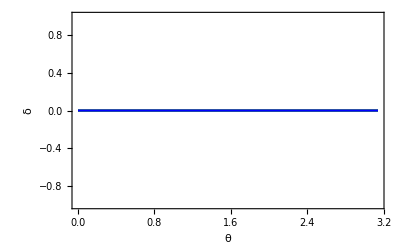

discordAtoBC optimal basis θ1=2.1595, discord(A:BC)=0

deltanewdiscord [Blue] optimal basis:{1.5708,2.74889,2.74889,-1.11022×10^-15}

deltanewdiscord

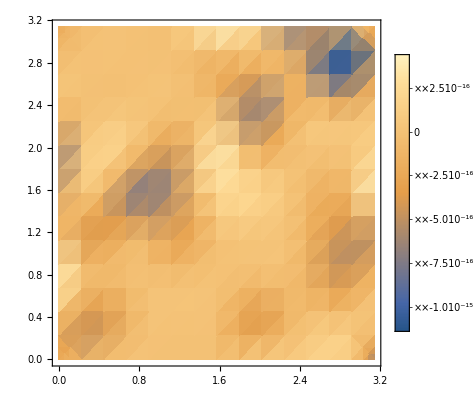

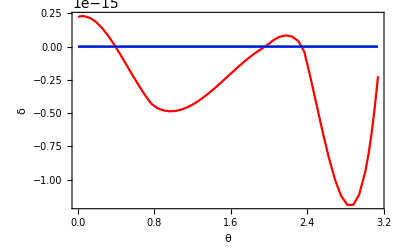

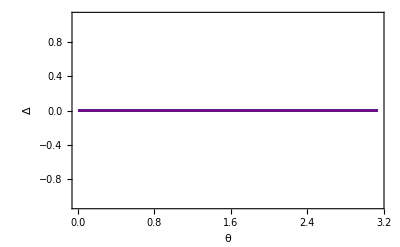

μ=0.1

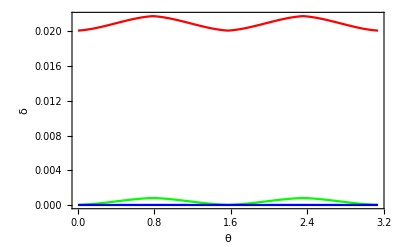

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.020089

deltanewdiscord [Blue] optimal basis:{2.3562,2.74889,0.3927,0.0279692}

deltanewdiscord

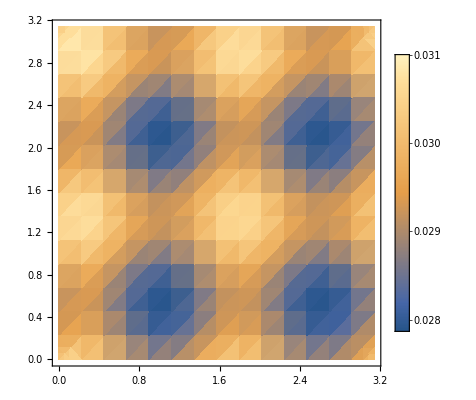

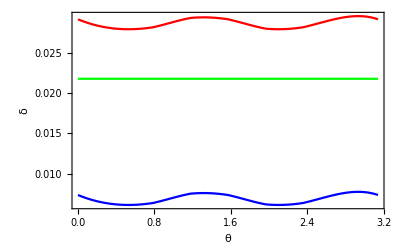

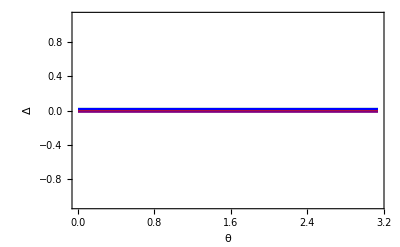

μ=0.2

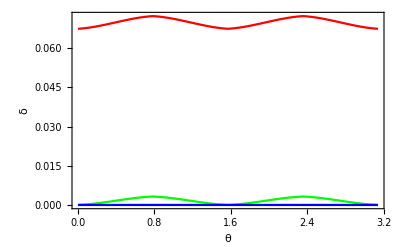

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.0674363

deltanewdiscord [Blue] optimal basis:{0.785399,1.9635,2.74889,0.0954158}

deltanewdiscord

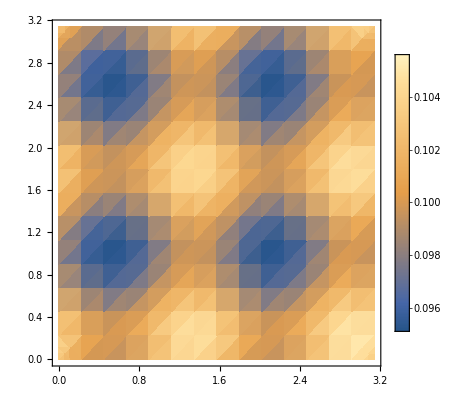

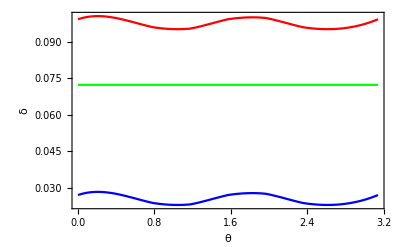

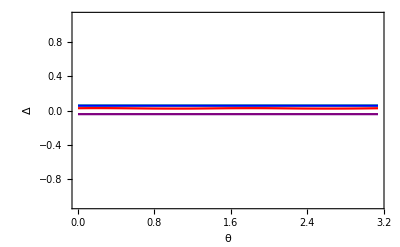

μ=0.3

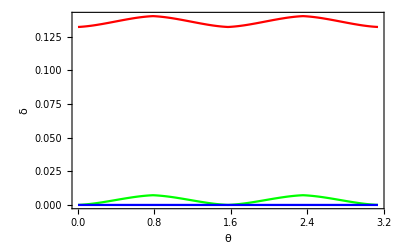

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.132329

deltanewdiscord [Blue] optimal basis:{2.3562,1.1781,1.9635,0.189639}

deltanewdiscord

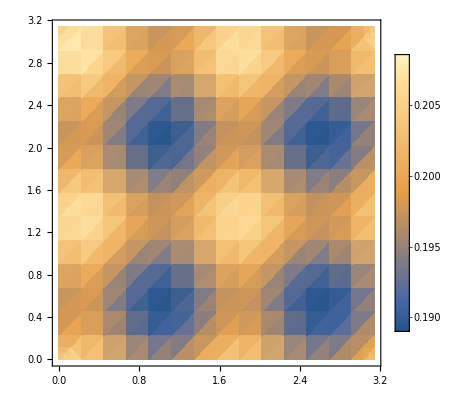

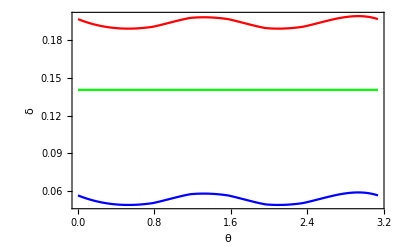

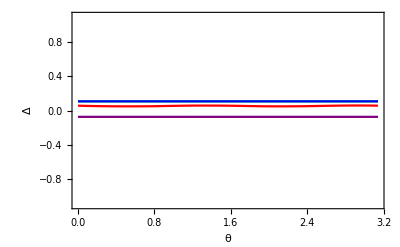

μ=0.4

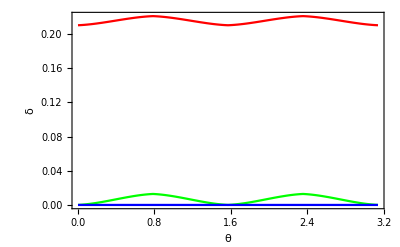

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.2104

deltanewdiscord [Blue] optimal basis:{2.3562,2.74889,0.3927,0.304925}

deltanewdiscord

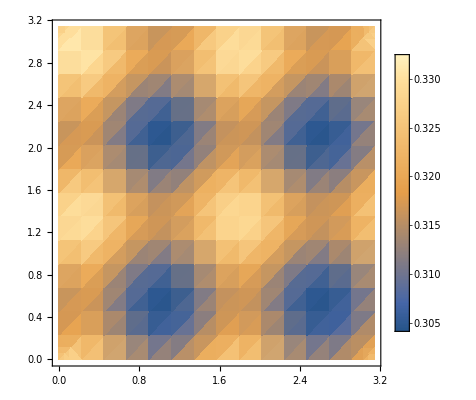

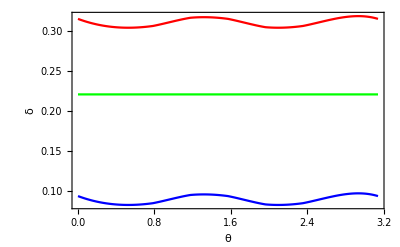

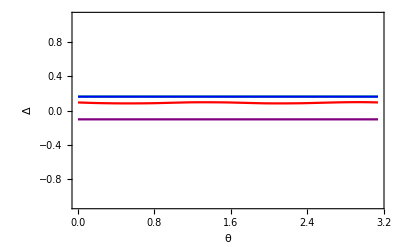

μ=0.5

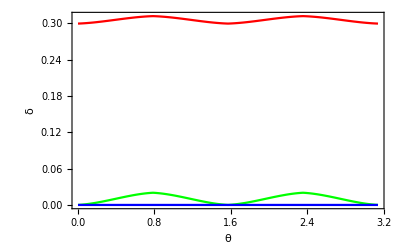

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.299427

deltanewdiscord [Blue] optimal basis:{0.785399,0.3927,2.74889,0.438604}

deltanewdiscord

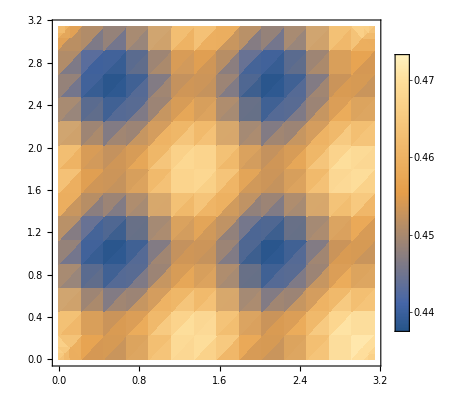

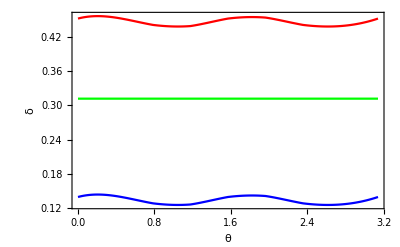

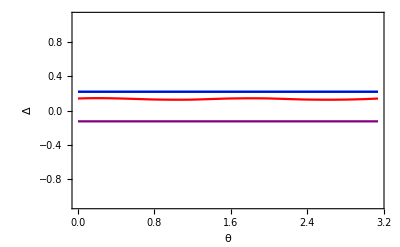

μ=0.6

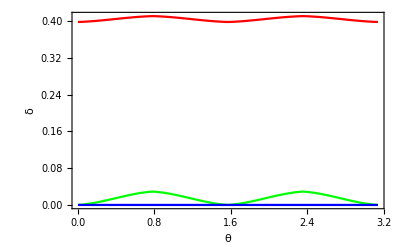

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.398338

deltanewdiscord [Blue] optimal basis:{2.3562,1.1781,0.3927,0.589851}

deltanewdiscord

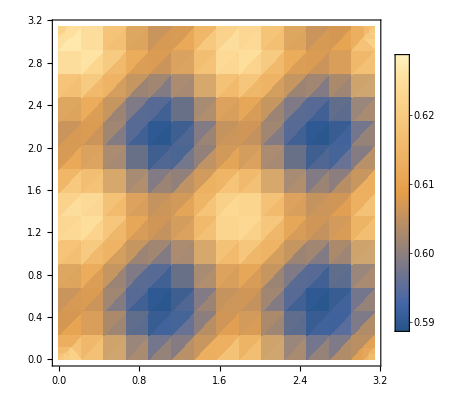

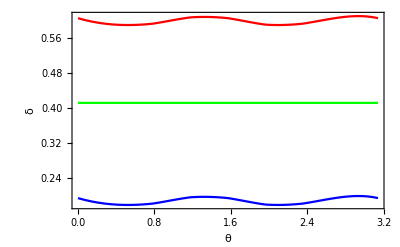

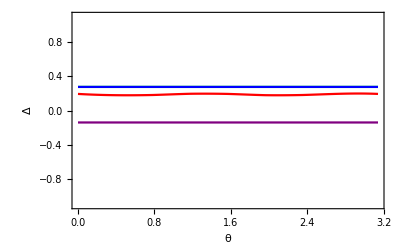

μ=0.7

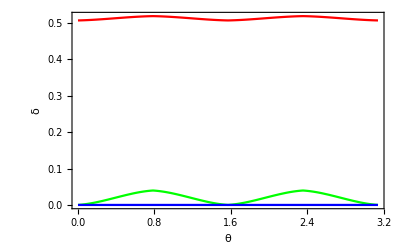

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.506913

deltanewdiscord [Blue] optimal basis:{2.3562,1.1781,1.9635,0.759491}

deltanewdiscord

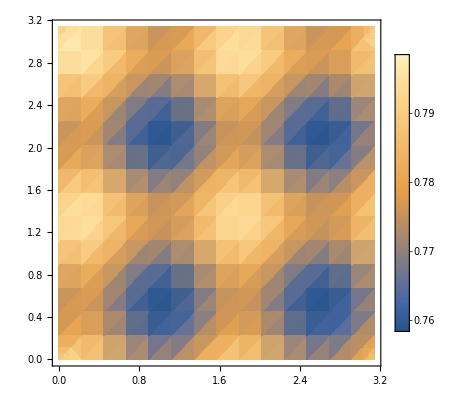

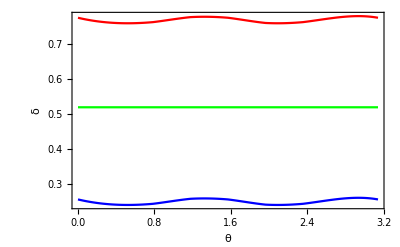

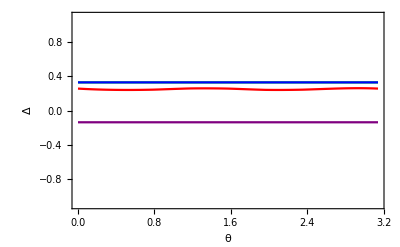

μ=0.8

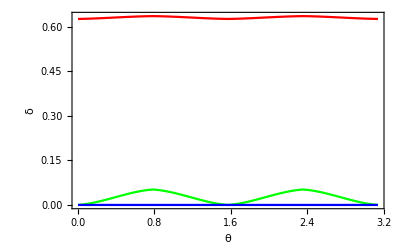

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.625903

deltanewdiscord [Blue] optimal basis:{0.785399,0.3927,2.74889,0.950664}

deltanewdiscord

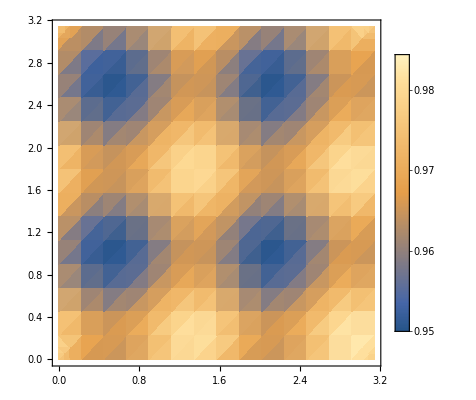

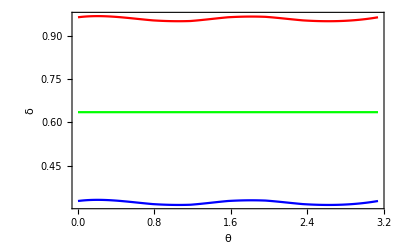

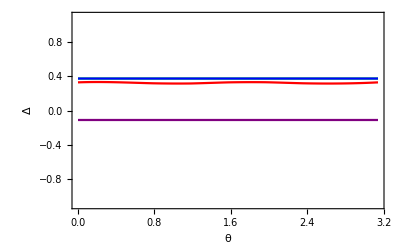

μ=0.9

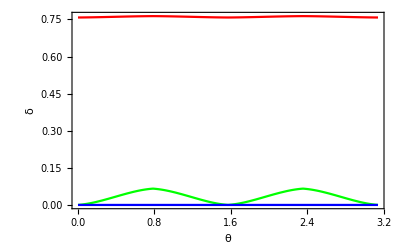

discordAtoBC optimal basis θ1=0., discord(A:BC)=0.758

deltanewdiscord [Blue] optimal basis:{2.3562,1.1781,1.9635,1.17188}

deltanewdiscord

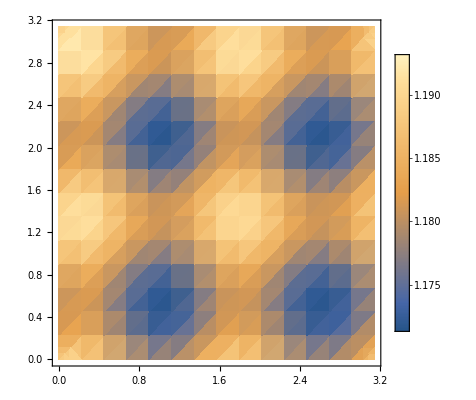

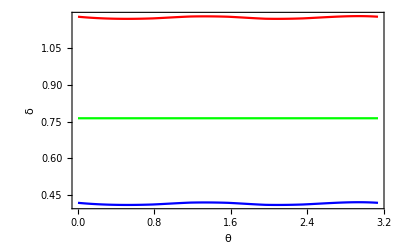

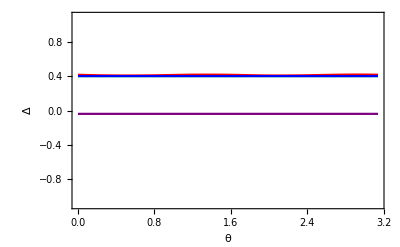

μ=1.

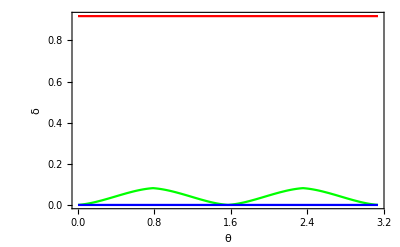

discordAtoBC optimal basis θ1=2.1595, discord(A:BC)=0.918296

deltanewdiscord [Blue] optimal basis:{2.3562,0.3927,1.1781,1.46834}

deltanewdiscord

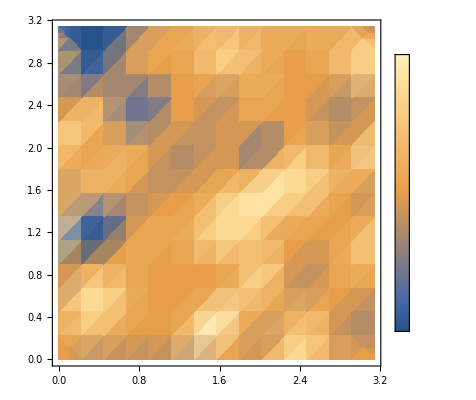

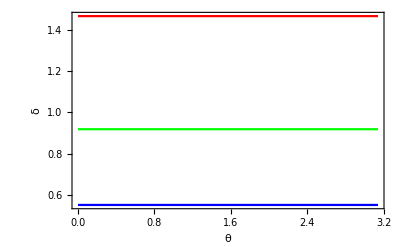

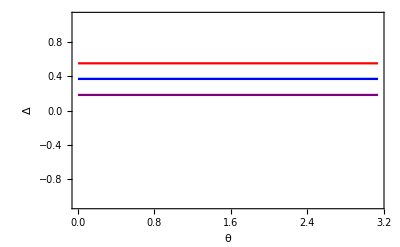

```mathematica
μmin=0.0;
μmax=1.0;
nomupoints=10;
ϵ=0.000001;
nopoints=32;
θmin=ϵ;
θmax=Pi+ϵ;
ϕ1=0;
ϕ2=0;
ϕ3=0;
deltanewdiscordmulist={};
D2ABmulist={};
D2ACmulist={};
D3mulist={};
discordAtoBCmulist={};
discordBtoCmulist={};

For[μ=μmin,μ≤μmax,μ=μ+(μmax-μmin)/nomupoints,
Print["μ=",μ];
dAtoBClist={};
dAlist={};
dBlist={};
For[θ1=θmin,θ1≤θmax,θ1=θ1+N[(θmax-θmin)/nopoints],
SABC=entropy[rhoabc];
SBC=entropy[rhobc];
SA=entropy[rhoa];
SABCM=entropy[rhoabcM1];
SBCM=entropy[rhobcM1];
SAM=entropy[rhoaM1];

dAtoBC=SABCM-SAM-SBCM-(SABC-SA-SBC);
dSA=SAM-SA;
dSB=SBCM-SBC;

dAtoBClist=Append[dAtoBClist,{θ1,Chop[dAtoBC]}];
dAlist=Append[dAlist,{θ1,Chop[dSA]}];
dBlist=Append[dBlist,{θ1,Chop[dSB]}];
];
dAtoBCfunc=Interpolation[dAtoBClist];
dAfunc=Interpolation[dAlist];
dBfunc=Interpolation[dBlist];

p2=Plot[{dAtoBCfunc[θ1],dAfunc[θ1],dBfunc[θ1]},{θ1,θmin,θmax},PlotStyle->{Red,Green,Blue,Purple,Cyan,Orange},PlotRange->All,FrameLabel->{"θ","δ"}];
Print[p2];
Clear[θ1];
optsol=NMinimize[{dAtoBCfunc[θ1],θ1>0,θ1<Pi},{θ1}];
θ1min=θ1/.optsol[[2]][[1]];
discordAtoBC=Chop[optsol[[1]]];
Print["discordAtoBC optimal basis θ1=",θ1min,", discord(A:BC)=",discordAtoBC];


dAtoBClist={};
dBtoClist={};
discordAtoBClist={};
discordBtoClist={};
deltanewdiscordlist={};
templist={};
D2ABlist={};
D2AClist={};
D3list={};
nopoints=8;
For[θ1=θmin,θ1≤θmax,θ1=θ1+N[(θmax-θmin)/nopoints],
For[θ2=θmin,θ2≤θmax,θ2=θ2+N[(θmax-θmin)/nopoints],
For[θ3=θmin,θ3≤θmax,θ3=θ3+N[(θmax-θmin)/nopoints],
SABC=entropy[rhoabc];
SAB=entropy[rhoab];
SAC=entropy[rhoac];
SBC=entropy[rhobc];
SA=entropy[rhoa];
SB=entropy[rhob];
SC=entropy[rhoc];

SABCM1=entropy[rhoabcM1];
SABM1=entropy[rhoabM1];
SACM1=entropy[rhoacM1];
SBCM1=entropy[rhobcM1];
SAM1=entropy[rhoaM1];
SBM1=entropy[rhobM1];
SCM1=entropy[rhocM1];

SABCM2=entropy[rhoabcM2];
SABM2=entropy[rhoabM2];
SACM2=entropy[rhoacM2];
SBCM2=entropy[rhobcM2];
SAM2=entropy[rhoaM2];
SBM2=entropy[rhobM2];
SCM2=entropy[rhocM2];

dAtoBC=SABCM1-SAM1-SBCM1-(SABC-SA-SBC);
discordAtoBC=SABCM1-SAM1-(SABC-SA);
dBtoC=SABCM2-SABM2-SACM2-(SABCM1-SABM1-SACM1);
discordBtoC=SABCM2-SABM2-(SABCM1-SABM1);
newdiscord=SABCM2-SABC-SABM2+SABM1-SAM2+SA;
D2AB=(SAC-SABC)-(SACM1-SABCM1);
D2AC=(SAB-SABC)-(SABM1-SABCM1);
D3=(SABC-SAB-SAC+SA)-(SABCM1-SABM1-SACM1+SAM1);



dAtoBClist=Append[dAtoBClist,{θ1,θ2,θ3,Chop[dAtoBC]}];
discordAtoBClist=Append[discordAtoBClist,{θ1,θ2,θ3,Chop[discordAtoBC]}];
dBtoClist=Append[dBtoClist,{θ1,θ2,θ3,Chop[dBtoC]}];
discordBtoClist=Append[discordBtoClist,{θ1,θ2,θ3,Chop[discordBtoC]}];
deltanewdiscordlist=Append[deltanewdiscordlist,{θ1,θ2,θ3,newdiscord}];
D2ABlist=Append[D2ABlist,{θ1,θ2,θ3,Chop[D2AB]}];
D2AClist=Append[D2AClist,{θ1,θ2,θ3,Chop[D2AC]}];
D3list=Append[D3list,{θ1,θ2,θ3,Chop[D3]}];

(*templist=Append[templist,{SABM2-SABM1-(SBM2-SBM1)}];*)


];
];
];

dAtoBCfunc=Interpolation[dAtoBClist];
dBtoCfunc=Interpolation[dBtoClist];
discordAtoBCfunc=Interpolation[discordAtoBClist];
discordBtoCfunc=Interpolation[discordBtoClist];
deltanewdiscordfunc=Interpolation[deltanewdiscordlist];
D2ABfunc=Interpolation[D2ABlist];
D2ACfunc=Interpolation[D2AClist];
D3func=Interpolation[D3list];



newdiscordsol=MinimalBy[deltanewdiscordlist,Last][[1]];
Print["deltanewdiscord [Blue] optimal basis:",newdiscordsol];


θ1min=newdiscordsol[[1]];
θ2min=newdiscordsol[[2]];
θ3min=newdiscordsol[[3]];


Print["deltanewdiscord"];
p1=DensityPlot[deltanewdiscordfunc[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];

(*Print["dAtoBCfunc"];
p1=DensityPlot[dAtoBCfunc[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];
Print["dBtoCfunc"];
p1=DensityPlot[dBtoCfunc[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];
Print["discordAtoBCfunc"];
p1=DensityPlot[discordAtoBCfunc[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];
Print["discordBtoCfunc"];
p1=DensityPlot[discordBtoCfunc[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];
Print["D2ABfunc"];
p1=DensityPlot[D2ABfunc[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];
Print["D2ACfunc"];
p1=DensityPlot[D2ACfunc[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];
Print["D3func"];
p1=DensityPlot[D3func[θ1min,θ2,θ3],{θ2,θmin,θmax},{θ3,θmin,θmax},PlotLegends->Automatic];
Print[p1];*)



p2=Plot[{deltanewdiscordfunc[θ1min,θ2min,θ3],discordAtoBCfunc[θ1min,θ2min,θ3],discordBtoCfunc[θ1min,θ2min,θ3]},{θ3,θmin,θmax},PlotStyle->{Red,Green,Blue,Purple,Cyan,Orange},PlotRange->All,FrameLabel->{"θ","δ"}];
Print[p2];
p3=Plot[{discordBtoCfunc[θ1min,θ2min,θ3],D2ABfunc[θ1min,θ2min,θ3],D2ACfunc[θ1min,θ2min,θ3],D3func[θ1min,θ2min,θ3]},{θ3,θmin,θmax},PlotStyle->{Red,Green,Blue,Purple,Cyan,Orange},PlotRange->{-1.1,1.1},FrameLabel->{"θ","Δ"}];
Print[p3];

deltanewdiscordmulist=Append[deltanewdiscordmulist,{μ,deltanewdiscordfunc[θ1min,θ2min,θ3min]}];
D2ABmulist=Append[D2ABmulist,{μ,D2ABfunc[θ1min,θ2min,θ3min]}];
D2ACmulist=Append[D2ACmulist,{μ,D2ACfunc[θ1min,θ2min,θ3min]}];
D3mulist=Append[D3mulist,{μ,D3func[θ1min,θ2min,θ3min]}];
discordAtoBCmulist=Append[discordAtoBCmulist,{μ,discordAtoBCfunc[θ1min,θ2min,θ3min]}];
discordBtoCmulist=Append[discordBtoCmulist,{μ,discordBtoCfunc[θ1min,θ2min,θ3min]}];


];
```

#### Werner GHZ

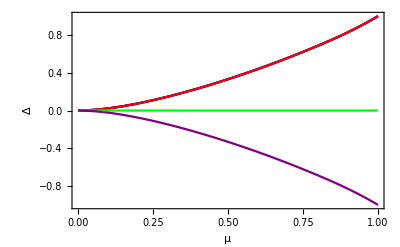

```mathematica
deltanewdiscordmulist={{0.,-1.5543122344752194*^-15},{0.1,0.02255950803217832},{0.2,0.0754887502166286},{0.30000000000000004,0.14762905706984553},{0.4,0.23395036619028597},{0.5,0.33187775400822783},{0.6,0.4401373713535557},{0.7,0.558383202134537},{0.7999999999999999,0.6872817334119385},{0.8999999999999999,0.8294705467767908},{0.9999999999999999,1.0000000000004414}};
D2ABmulist={{0.,0.},{0.1,0.022559508032073294},{0.2,0.07548875021623047},{0.30000000000000004,0.14762905706898377},{0.4,0.2339503661887865},{0.5,0.33187775400590724},{0.6,0.44013737135018727},{0.7,0.5583832021298212},{0.7999999999999999,0.6872817334054},{0.8999999999999999,0.8294705467674136},{0.9999999999999999,0.9999999999995569}};
D2ACmulist={{0.,0.},{0.1,0.022559508032073294},{0.2,0.07548875021623047},{0.30000000000000004,0.14762905706898377},{0.4,0.2339503661887865},{0.5,0.33187775400590724},{0.6,0.44013737135018727},{0.7,0.5583832021298212},{0.7999999999999999,0.6872817334054},{0.8999999999999999,0.8294705467674136},{0.9999999999999999,0.9999999999995569}};
D3mulist={{0.,0.},{0.1,-0.022559508032044207},{0.2,-0.07548875021611368},{0.30000000000000004,-0.1476290570687162},{0.4,-0.23395036618829756},{0.5,-0.33187775400511477},{0.6,-0.4401373713489871},{0.7,-0.5583832021280695},{0.7999999999999999,-0.687281733402864},{0.8999999999999999,-0.8294705467635902},{0.9999999999999999,-0.9999999999991142}};
discordAtoBCmulist={{0.,0.},{0.1,0.022559508032102382},{0.2,0.07548875021634727},{0.30000000000000004,0.14762905706925133},{0.4,0.23395036618927545},{0.5,0.3318777540066997},{0.6,0.4401373713513874},{0.7,0.5583832021315729},{0.7999999999999999,0.687281733407936},{0.8999999999999999,0.829470546771237},{0.9999999999999999,0.9999999999999997}};
discordBtoCmulist={{0.,0.},{0.1,0.},{0.2,0.},{0.30000000000000004,6.938893903907228*^-18},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.7999999999999999,0.},{0.8999999999999999,5.551115123125783*^-17},{0.9999999999999999,0.}};
deltanewdiscordmuint=Interpolation[deltanewdiscordmulist];
D2ABmuint=Interpolation[D2ABmulist];
D2ACmuint=Interpolation[D2ACmulist];
D3muint=Interpolation[D3mulist];
discordAtoBCmuint=Interpolation[discordAtoBCmulist];
discordBtoCmuint=Interpolation[discordBtoCmulist];
Plot[{deltanewdiscordmuint[x],D2ABmuint[x],D2ACmuint[x],discordBtoCmuint[x],D3muint[x]},{x,0,1},PlotStyle->{Black,Blue,Red,Green,Purple},FrameLabel->{"μ","Δ"},PlotRange->All]
```

#### Werner W

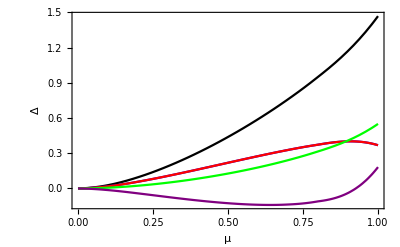

```mathematica
deltanewdiscordmulist={{0.,-1.1102230246251567*^-15},{0.1,0.02796915933710009},{0.2,0.09541580620701429},{0.30000000000000004,0.18963882391321918},{0.4,0.3049254998185662},{0.5,0.438603783892888},{0.6,0.5898508004134426},{0.7,0.7594909106215282},{0.7999999999999999,0.9506642611573661},{0.8999999999999999,1.1718789163291041},{0.9999999999999999,1.468343593637545}};
D2ABmulist={{0.,0.},{0.1,0.017887006005387285},{0.2,0.057174829744527145},{0.30000000000000004,0.1069293756779417},{0.4,0.16191409094161302},{0.5,0.21886059848379924},{0.6,0.2751230434762284},{0.7,0.32783820077473846},{0.7999999999999999,0.37278949346685875},{0.8999999999999999,0.4011679974769262},{0.9999999999999999,0.36824807447143293}};
D2ACmulist={{0.,0.},{0.1,0.017887006005387285},{0.2,0.057174829744527145},{0.30000000000000004,0.1069293756779417},{0.4,0.16191409094161302},{0.5,0.21886059848379924},{0.6,0.2751230434762284},{0.7,0.32783820077473846},{0.7999999999999999,0.37278949346685875},{0.8999999999999999,0.4011679974769262},{0.9999999999999999,0.36824807447143293}};
D3mulist={{0.,0.},{0.1,-0.014016149715039061},{0.2,-0.04206927729109},{0.30000000000000004,-0.07345524029885575},{0.4,-0.10274004132180536},{0.5,-0.12597468630979425},{0.6,-0.13915812114645099},{0.7,-0.1369309291024714},{0.7999999999999999,-0.11021900993191258},{0.8999999999999999,-0.03879739280714589},{0.9999999999999999,0.18179968511162325}};
discordAtoBCmulist={{0.,0.},{0.1,0.02175786229573551},{0.2,0.07228038219796429},{0.30000000000000004,0.14040351105702786},{0.4,0.22108814056142068},{0.5,0.31174651065780434},{0.6,0.4110879658060058},{0.7,0.5187454724470055},{0.7999999999999999,0.6353599770018049},{0.8999999999999999,0.7635386021467065},{0.9999999999999999,0.9182958340544892}};
discordBtoCmulist={{0.,0.},{0.1,0.006211297041364583},{0.2,0.023135424009049776},{0.30000000000000004,0.04923531285619154},{0.4,0.08383735925714575},{0.5,0.12685727323508367},{0.6,0.1787628346074368},{0.7,0.24074543817452265},{0.7999999999999999,0.31530428415556133},{0.8999999999999999,0.4083403141823978},{0.9999999999999999,0.5500477595830556}};
deltanewdiscordmuint=Interpolation[deltanewdiscordmulist];
D2ABmuint=Interpolation[D2ABmulist];
D2ACmuint=Interpolation[D2ACmulist];
D3muint=Interpolation[D3mulist];
discordAtoBCmuint=Interpolation[discordAtoBCmulist];
discordBtoCmuint=Interpolation[discordBtoCmulist];
Plot[{deltanewdiscordmuint[x],D2ABmuint[x],D2ACmuint[x],discordBtoCmuint[x],D3muint[x]},{x,0,1},PlotStyle->{Black,Blue,Red,Green,Purple},FrameLabel->{"μ","Δ"},PlotRange->All]
```